# Typical examples

```mathematica
SetDirectory[NotebookDirectory[]]; (*set directory*)
```

Add the folder(s) containing the current package as well as NC package to $Path

```mathematica
AppendTo[$Path,"/Users/yumish/Dropbox/a_recherche/mathematica_all/mathematica_packages/"];
<<NC` (*load NCAlgebra*)
<<NCAlgebra`
<<PolynomialsOfRandomMatrices`
```

NC::Directory: You are using the version of NCAlgebra which is found in: "/Users/yumish/Library/CloudStorage/Dropbox/a_recherche/mathematica_all/mathematica_packages/NC/".

NCAlgebra::SmallCapSymbolsNonCommutative: All lower cap single letter symbols (e.g. a,b,c,...) were set as noncommutative.

```mathematica
$ContextPath (* check if the packages have been loaded *)
```

{PolynomialsOfRandomMatrices`,NCAlgebra`,NC`,NCOutput`,Notation`,NCDeprecated`,NCSimplifyRational`,NCMatrixDecompositions`,NCSelfAdjoint`,NCOptions`,NCDiff`,NCCollect`,NCPolynomial`,NCPolyInterface`,NCPoly`,MatrixDecompositions`,NCUtil`,NCReplace`,NCDot`,NCTr`,NonCommutativeMultiply`,Wolfram`Chatbook`,System`,Global`}

## 1. Generating random matrices, random variables, polynomials

## 1.1 Generate a complex Ginibre matrix

Ginibre[n] generates a complex nxn matrix with iid entries having mean 0 and variance 1

```mathematica
Y=Ginibre[1000];
```

Plot the eigenvalues of Y

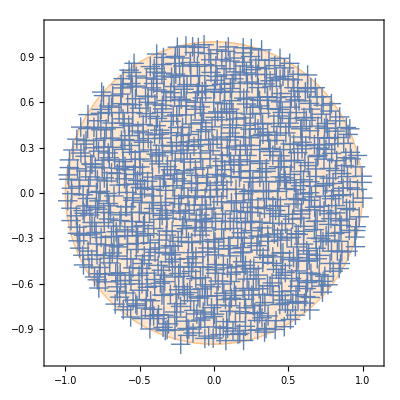

```mathematica
ev=Eigenvalues[Y];
Show[ContourPlot[x^2+y^2,{x,-1,1},{y,-1,1},Contours->{1},ContourStyle->Directive[Orange,Thick],ColorFunction->(If[#1>1/2,White,LightOrange]&)],ListPlot[Table[{Re[ev[[j]]],Im[ev[[j]]]},{j, Length[ev]}], AspectRatio->1,PlotMarkers->{"+",20}],PlotRange->{{-1.1,1.1},{-1.1,1.1}},FrameTicksStyle->{{FontSize->16,FontFamily->"Serif"},{FontSize->16,FontFamily->"Serif"}},ImageSize->400,Axes->False,Frame->True]
```

## 1.2 Generate a real Ginibre matrix

GinibreReal[n] generates a real nxn matrix with iid entries having mean 0 and variance 1

```mathematica
Y=GinibreReal[1000];
```

Plot the eigenvalues of Y

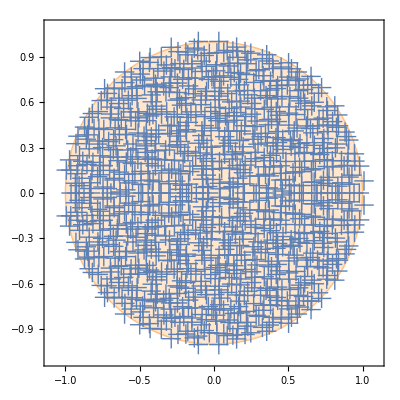

```mathematica
ev=Eigenvalues[Y];
Show[ContourPlot[x^2+y^2,{x,-1,1},{y,-1,1},Contours->{1},ContourStyle->Directive[Orange,Thick],ColorFunction->(If[#1>1/2,White,LightOrange]&)],ListPlot[Table[{Re[ev[[j]]],Im[ev[[j]]]},{j, Length[ev]}], AspectRatio->1,PlotMarkers->{"+",20}],PlotRange->{{-1.1,1.1},{-1.1,1.1}},FrameTicksStyle->{{FontSize->16,FontFamily->"Serif"},{FontSize->16,FontFamily->"Serif"}},ImageSize->400,Axes->False,Frame->True]
```

## 1.3 Generate iid numbers uniformly distributed on the unit disk

IIDUnitDisk[n] generates a list of n complex numbers uniformly distributed on the unit disk

```mathematica
L=IIDUnitDisk[1000];
```

Plot these numbers

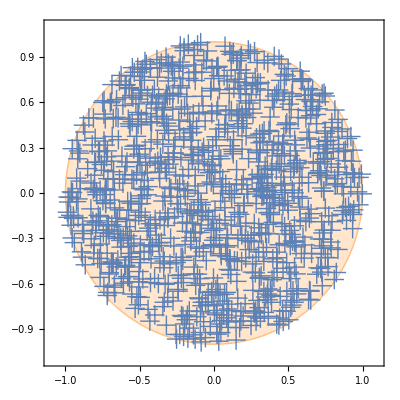

```mathematica
Show[ContourPlot[x^2+y^2,{x,-1,1},{y,-1,1},Contours->{1},ContourStyle->Directive[Orange,Thick],ColorFunction->(If[#1>1/2,White,LightOrange]&)],ListPlot[Table[{Re[L[[j]]],Im[L[[j]]]},{j, Length[L]}], AspectRatio->1,PlotMarkers->{"+",20}],PlotRange->{{-1.1,1.1},{-1.1,1.1}},FrameTicksStyle->{{FontSize->16,FontFamily->"Serif"},{FontSize->16,FontFamily->"Serif"}},ImageSize->400,Axes->False,Frame->True]
```

## 1.4 Generate a complex Wigner matrix

Wigner[n] returns an nxn Wigner matix with complex entries with variance 1/n

```mathematica
X=Wigner[1000];
```

Plot the histogram of the eigenvalues of X

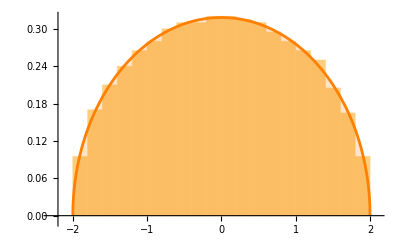

```mathematica
ev=Eigenvalues[X];
Show[Histogram[ev,21,"PDF"],Plot[PDF[WignerSemicircleDistribution[2],x]//Evaluate,{x,-2,2},Exclusions->None,Filling->Axis,PlotStyle->{Orange}],PlotRange->{{-2.3,2.1},{-0.01,0.32}},AxesOrigin->{-2.2,0},TicksStyle->{{FontSize->16,FontFamily->"Serif"},{FontSize->16,FontFamily->"Serif"}},ImageSize->400]
```

## 1.5 Generate a real Wigner matrix

WignerReal[n] returns an nxn  Wigner matix with real entries with variance 1/n

```mathematica
X=WignerReal[3000];
```

Plot the histogram of the eigenvalues of X together with the circular law density

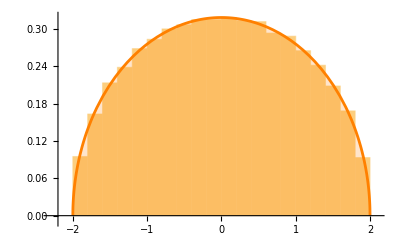

```mathematica
ev=Eigenvalues[X];
Show[Histogram[ev,21,"PDF"],Plot[PDF[WignerSemicircleDistribution[2],x]//Evaluate,{x,-2,2},Exclusions->None,Filling->Axis,PlotStyle->{Orange}],PlotRange->{{-2.3,2.1},{-0.01,0.32}},AxesOrigin->{-2.2,0},TicksStyle->{{FontSize->16,FontFamily->"Serif"},{FontSize->16,FontFamily->"Serif"}},ImageSize->400]
```

## 1.6 Generate an NC polynomial with random coefficients

Function GeneratePolynimial(VariableList,{t1,t2...},”Type”) generates polynomial with randomly chosen coefficients of type “Type” with ~t_1 terms of degree 1, t_2 terms of degree 2 etc, (maybe a bit more due to symmetrization) in variables from VariableList (in usual ordering i.e. x, y, xx, xy, yx, yy, xxx...). Type can be “Integer”(“ComplexInteger”) for (complex) integer coefficients, “Real” for real coefficients, “Complex” for complex. Note that z is always a special variable. Notice that x, y, ... are self-adjoint NC variables

```mathematica
GeneratePolynomial[{x,y,s},{3,5,8},"Integer"]
GeneratePolynomial[{x,y},{2,0,8},"Real"]
GeneratePolynomial[{x,y,s,t},{0,16},"Complex"]
GeneratePolynomial[{x,y},{1,3},"RealHighPrecision",20]
```

s-9 x-3 y-4 s**s+(s**x)/2+s**y+(x**s)/2+5 x**x-5 x**y+y**s-5 y**x-9 y**y+(5 s**x**x)/2-5 s**y**x+3 s**y**y+5 x**s**x+(5 x**x**s)/2-5 x**y**s+10 x**y**x+(3 x**y**y)/2+3 y**y**s+(3 y**y**x)/2

-4.33816 x-9.87095 y-2.08342 x**x**x+0.633351 x**x**y+3.86823 x**y**x-5.15181 x**y**y+0.633351 y**x**x-2.662 y**x**y-5.15181 y**y**x-0.554604 y**y**y

-2.8225 s**s-(1.93476+3.5265 ⅈ) s**t-(0.590392-2.10418 ⅈ) s**x+(0.714864-0.0797394 ⅈ) s**y-(1.93476-3.5265 ⅈ) t**s-0.344484 t**t-(1.82822+0.767759 ⅈ) t**x-(1.38097-0.454108 ⅈ) t**y-(0.590392+2.10418 ⅈ) x**s-(1.82822-0.767759 ⅈ) x**t-4.1526 x**x+(0.276001+0.240499 ⅈ) x**y+(0.714864+0.0797394 ⅈ) y**s-(1.38097+0.454108 ⅈ) y**t+(0.276001-0.240499 ⅈ) y**x-2.4347 y**y

2.45302790442351503 y+9.89558835789289717 x**x-3.54062462961321665 x**y-3.54062462961321665 y**x

## 2. MDE

## 2.1 Compute the value of the superoperator Γ obtained from a linearization matrix applied to some matrix R

SOperator2[Linearization,z,R] returns Γ[R], where Γ is the superoperator constructed from the Linearization matrix with spectral parameter z;

```mathematica
Linearization={{1-z,x,y},{x,0,-1},{y,-1,0}};
R={{1,1,3},{-2,0,1},{2,2,0}};
MatrixForm@SOperator2[Linearization,z,R]
```

(0. | -2. | 2.
1. | 1. | 0.
3. | 0. | 1.)

## 2.2 Solve MDE at a point

### 2.2.1 Solve MDE at a point by specifying the S-operator

IterativelySolveMDE[SOperator, ConstantMatrix, DirectionMatrix, z, M0, K, ϵ] solves the MDE -M^{-1} = zJ-A+S[M]  at a fixed spectral parameter z.  SOperator is the Superoperator S given as a function with matrices as input and output, ConstantMatrix is the constant matrix A,  DirectionMatrix is the direction matrix J, z is the spectral parameter, M0 is the initial condition for the iteration, K is the maximum number of steps in the iteration, ϵ is the accuracy.

Preparation. In the example below we define the matrix Linearization, which is the linearization of the polynomial 1+XY+YX in Wigner matrices X and Y. From that get the ConstantMatrix=LL0, DirectionMatrix=JJ, SOperator=SSOperator. We also fix K=KK and ϵ=ϵϵ.

```mathematica
Clear[z,Linearization,VVariableList,LL0,LL,JJ,SSOperator,KK,MM,ϵϵ];Linearization={{1-z,x,y},{x,0,-1},{y,-1,0}};VVariableList=DeleteCases[DeleteDuplicates[Cases[Linearization,_Symbol,Infinity]],z];
LL0=N[Linearization/.Join[Table[VVariableList[[i]]->0,{i,Length[VVariableList]}],{z->0}]];
LL=N[Table[D[Linearization,VVariableList[[i]]],{i,Length[VVariableList]}]];
JJ=-N[D[Linearization,z]];
SSOperator[R_]:=Total[Table[LL[[i]].R.LL[[i]],{i,Length[LL]}]];

KK=500; ϵϵ=0.0001;
```

Now we solve the MDE with the above parameters at point z = 0.1*ⅈ with the initial condition for the iteration M0 = ⅈ*I.

```mathematica
MM=IterativelySolveMDE[SSOperator,LL0,JJ,0.1*I,I*IdentityMatrix[Length[JJ]],KK,ϵϵ];
MatrixForm@MM
```

(0.388465+0.595352 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.115614+0.539115 ⅈ | -0.723975-0.278285 ⅈ
0.+0. ⅈ | -0.723975-0.278285 ⅈ | 0.115614+0.539115 ⅈ)

### 2.2.2 Solve MDE at a point from the given Linearization matrix

IterativelySolveMDE2[Linearization,z,Z,M0,K,ϵ] solves the MDE -M^{-1} = zJ-A+S[M] at a fixed spectral parameter z=Z; exactly as IterativelySolveMDE, but SOperator,ConstantMatrix and DirectionMatrix are determined from Linearization; z is the spectral parameter (variable), Z is the value of the spectral parameter (number), K is the maximum number of steps in the iteration, ϵ is the accuracy. The advantage is that it need less preparation, only the linearization matrix

Preparation.

```mathematica
Linearization={{1-z,x,y},{x,0,-1},{y,-1,0}};
 KK=5000; ϵϵ=0.0001;
```

Once the Linearization is defined, we can directly apply IterativelySolveMDE2[Linearization,z,Z,M0,K,ϵ] with M0=ⅈI

```mathematica
MM=IterativelySolveMDE2[Linearization,z,0.1*I,ⅈ*IdentityMatrix[Length[Linearization]],KK,ϵϵ];
MatrixForm@MM
```

(0.388465+0.595352 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.115614+0.539115 ⅈ | -0.723975-0.278285 ⅈ
0.+0. ⅈ | -0.723975-0.278285 ⅈ | 0.115614+0.539115 ⅈ)

## 2.3 Solve MDE on an interval

### 2.3.1 Solve MDE on an interval by specifying the S-operator

IterativelySolveMDEonInterval[SOperator,ConstantMatrix,DirectionMatrix,E1,E2,η,L,K,ϵ] solves the MDE along a parameter interval E+iη with E ∈ [E_ 1,E_ 2]; Arguments are the same as for IterativelySolveMDE; the extra arguments are E1 (left edge of the interval), E2 (right edge of the interval), η (Fixed value for Im[z]), L (Number of points in the interval on which the solution is evaluated). The function returns a list of L+1 pairs {E,M(E+ⅈ η)}, where E are the numbers between E1 and E2, and M(E+ⅈη) is the solution to the MDE.

Preparation. In the example below we define the matrix Linearization, which is the linearization of the polynomial 1+XY+YX in Wigner matrices X and Y. From that get the ConstantMatrix=LL0, DirectionMatrix=JJ, SOperator=SSOperator. We also fix K=KK and ϵ=ϵϵ. Those are needed to use IterativelySolveMDE. Then we fix E1=EE1, E2=EE2, η=ηη and  L=LLPoints.

```mathematica
Clear[z,Linearization,VVariableList,LL0,LL,JJ,SSOperator,KK,MM,ϵϵ];Linearization={{1-z,x,y},{x,0,-1},{y,-1,0}};VVariableList=DeleteCases[DeleteDuplicates[Cases[Linearization,_Symbol,Infinity]],z];
LL0=N[Linearization/.Join[Table[VVariableList[[i]]->0,{i,Length[VVariableList]}],{z->0}]];
LL=N[Table[D[Linearization,VVariableList[[i]]],{i,Length[VVariableList]}]];
JJ=-N[D[Linearization,z]];
SSOperator[R_]:=Total[Table[LL[[i]].R.LL[[i]],{i,Length[LL]}]];

KK=5000; ϵϵ=0.0001;
EE1=-2.5; EE2=4.5; ηη=0.0001; LLPoints = 1000;
```

Now we solve the corresponding MDE on the interval [-2.5, 4.5]

```mathematica
MM=IterativelySolveMDEonInterval[SSOperator,LL0,JJ,EE1,EE2,ηη,LLPoints,KK,ϵϵ];
```

Now we simulate the matrix P =1+XY+YX with X and Y being independent (complex) Wigner matrices.

```mathematica
X=Wigner[4000];Y=Wigner[4000];P=IdentityMatrix[4000]+X.Y+Y.X;
ev=Eigenvalues[P];
```

And compare the plots of the theoretical Density of States from the solution to the MDE, and  the histogram of the eigenvalues of 1+XY+YX

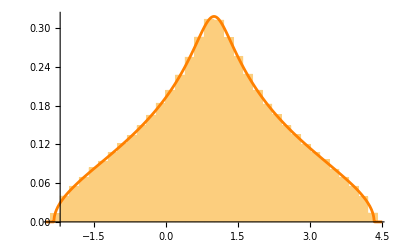

```mathematica
Show[Histogram[Re[ev],Automatic,"PDF"],ListLinePlot[
Table[{MM[[i,1]],Im[MM[[i,2]][[1,1]]]/Pi},{i,Length[MM]}],
PlotRange->{0,1.02 Max[Table[Im[MM[[i,2]][[1,1]]],{i,Length[MM]}]]},PlotStyle->{Orange}],AxesOrigin->{-2.2,0},TicksStyle->{{FontSize->16,FontFamily->"Serif"},{FontSize->16,FontFamily->"Serif"}},ImageSize->400]
```

### 2.3.2 Solve MDE on an interval using the given Linearization matrix

IterativelySolveMDEonInterval2[Linearization,z,E1,E2,η,L,K,ϵ] solves the MDE along a parameter interval E+iη with E ∈ [E_ 1,E_ 2]; Arguments are the same as for IterativelySolveMDE2; the extra arguments are E1 (left edge of the interval), E2 (right edge of the interval), η (Fixed value for Im[z]), L (Number of points in the interval on which the solution is evaluated). The function returns a list of L+1 pairs {E,M(E+ⅈ η)}, where E are the numbers between E1 and E2, and M(E+ⅈη) is the solution to the MDE. The advantage compared to IterativelySolveMDEonInterval is that the preparation is much shorter.

```mathematica
Linearization={{1-z,x,y},{x,0,-1},{y,-1,0}};
KK=5000; ϵϵ=0.0001;
EE1=-2.5; EE2=4.5; ηη=0.0001; LLPoints = 1000;
```

Once the Linearization is defined and the parameters are given, we can apply IterativelySolveMDEonInterval2

```mathematica
MM=IterativelySolveMDEonInterval2[Linearization,z,EE1,EE2,ηη,LLPoints,KK,ϵϵ];
```

Now we simulate the matrix P =1+XY+YX with X and Y being independent (complex) Wigner matrices.

```mathematica
X=Wigner[4000];Y=Wigner[4000];P=IdentityMatrix[4000]+X.Y+Y.X;
ev=Eigenvalues[P];
```

And compare the plots of the theoretical Density of States from the solution to the MDE, and  the histogram of the eigenvalues of 1+XY+YX

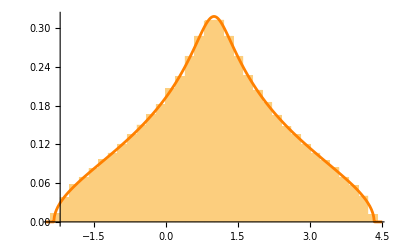

```mathematica
Show[Histogram[Re[ev],Automatic,"PDF"],ListLinePlot[
Table[{MM[[i,1]],Im[MM[[i,2]][[1,1]]]/Pi},{i,Length[MM]}],
PlotRange->{0,1.02 Max[Table[Im[MM[[i,2]][[1,1]]],{i,Length[MM]}]]},PlotStyle->{Orange}],AxesOrigin->{-2.2,0},TicksStyle->{{FontSize->16,FontFamily->"Serif"},{FontSize->16,FontFamily->"Serif"}},ImageSize->400]
```

## 3. Linearization of polynomials

## 3.1 Construct the big linearization of a given polynomial

BigLinearization[polynomial] constructs the initial (big) linearization of the polynomial. Our consideration are only for self-adjoint elements x_i.
We call a linearization L=L_0+∑_i L_i⊗x_i of a polynomial p canonical when it satisfies L^{-1}[[1,1]]=1/p.
For a given canonical linearization, we may make it self-adjoint provided p is self-adjoint.

Basic example 1: Trivial linearizations of x and a constant 1.5

```mathematica
MatrixForm@BigLinearization[x]
MatrixForm@BigLinearization[1.5]
```

(x)

(1.5)

Basic example 2: Linearizations of monomials with coefficient 1

```mathematica
MatrixForm@BigLinearization[x**x]
MatrixForm@BigLinearization[x**y**x]
MatrixForm@BigLinearization[x**y**x*2]
```

(0 | x
x | -1)

(0 | 0 | x
0 | y | -1
x | -1 | 0)

(0 | 0 | √2 x
0 | y | -1
√2 x | -1 | 0)

Basic example 3: Linearizations of monomials with arbitrary coefficients

```mathematica
MatrixForm@BigLinearization[1.5x**x]
MatrixForm@BigLinearization[5 x**y**x]
```

(0 | 1.22474 x
1.22474 x | -1.)

(0 | 0 | √5 x
0 | y | -1
√5 x | -1 | 0)

Basic example 4: Linearizations of more compicated polynomials

```mathematica
MatrixForm@BigLinearization[y**y-2x**x]
MatrixForm@BigLinearization[5 x**y**x+x**y+y**x-z]
```

(0 | √2 x | y | √2 x | y
√2 x | 0 | 0 | 2 | 0
y | 0 | 0 | 0 | -2
√2 x | 2 | 0 | 0 | 0
y | 0 | -2 | 0 | 0)

(-z | x | y | 0 | √5 x | y | x | 0 | √5 x
x | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0
y | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 y | -2
√5 x | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0
y | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
x | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 y | -2 | 0 | 0 | 0 | 0
√5 x | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0)

## 3.2 Construct the minimal linearization of the given polynomial

Generating the canonical minimal linearization using the function MinimalLinearization[polynomial,Type,Precision(optional)] (important:  we add a constant 1 to all polynomials to ensure that the constant matrix of the big linearization is invertible), where 
		Type is either “Exact” for symbolic computations
			 or “MachinePrecision” for numeric with machine precision, 
			 or “HighPrecision” for numeric with higher than machine precision;
		 and “Precision” is the precision used in the numeric computations with higher than machine precision (⩾16).

Basic example 1: trivial minimal linearization:

```mathematica
MatrixForm@MinimalLinearization[1.5,"Exact"]
MatrixForm@N[MinimalLinearization[1+x,"MachinePrecision"],5]
```

(1.5)

(1.+1. x)

Basic example 2: minimal linearization for more complicated polynomials

```mathematica
MatrixForm@MinimalLinearization[1+y**y-2x**x,"Exact"]
N[MatrixForm@MinimalLinearization[1+5 x**y**x+x**y+y**x-z,"MachinePrecision"],5]
N[MatrixForm@MinimalLinearization[1+5 x**y**x+ⅈ*x**y-ⅈ*y**x-z,"HighPrecision",20],5]
```

(1 | 2 x | -y
2 x | 2 | 0
-y | 0 | -1)

(1.-1. z | 0.-1. y | 0.-1. x
0.-1. y | 0.+5. y | -1.
0.-1. x | -1. | 0.)

(1.-1. z | 1. ⅈ y | -1. ⅈ x
-1. ⅈ y | 5. y | -1. ⅈ
1. ⅈ x | 1. ⅈ | 0)

## 3.3 Indices that give the minimal linearization

Function MinimalIndices[polynomial, Type, Precision (optional)] returns indices that give the minimal linearization; it' s a modification of MinimalLinearization that returns only the set of indices and not the linearization itself

Basic example:

```mathematica
MinimalIndices[N[1+x**x+y**y],"MachinePrecision"]
MinimalIndices[N[1+x**y**x+y**y],"MachinePrecision"]
MinimalIndices[N[1+x**x**x-2*x**y**x+3*y**y-x**y-y**x+10*y],"MachinePrecision"]
```

{{},{1},{2}}

{{},{1},{2},{1,2}}

{{},{1},{2},{1,2}}

## 3.4 Reconstruction of the polynomial from the linearization

We use this function to check if the linearization was done correctly.  ReconstructPolynomial[linearization,”Check”(optional),polynomial1(optional),Precision(optional)] reconstructs polynomial2 from the given linearization and (if we choose “Check”) compares it with given polynomial1, i.e. compares the monomial coefficients and returns “Reconstruction OK” if the max difference is < 10^-5. The function returns (“Check”-> reconstructed polynomial2,conclusion, max difference of monomial coefficients between reconstructed polynomial2 and polynomial1; “NoCheck” -> reconstructed polynomial). If the reconstruction is not accurate enough, increase the precision

```mathematica
ReconstructPolynomial[MinimalLinearization[1+(1+ⅈ)x**y+(1-ⅈ)y**x,"Exact"]]
ReconstructPolynomial[MinimalLinearization[1+(1+ⅈ)x**y+(1-ⅈ)y**x,"Exact"],"Check",1+(1+ⅈ)x**y+(1-ⅈ)y**x]
ReconstructPolynomial[MinimalLinearization[1+x**x+y**x**y+x**y+y**x,"MachinePrecision"],"Check",1+x**x+y**x**y+x**y+y**x]
ReconstructPolynomial[MinimalLinearization[1+x**x+y**x**y+ⅈ*x**y-ⅈ*y**x,"HighPrecision",100],"Check",1+x**x+y**x**y+ⅈ*x**y-ⅈ*y**x,100]
```

{1.+(1.+1. ⅈ) x**y+(1.-1. ⅈ) y**x}

{1.+(1.+1. ⅈ) x**y+(1.-1. ⅈ) y**x,Reconstruction: OK,0}

{1.+1. x**x+1. x**y+1. y**x+1. y**x**y,Reconstruction: OK,5.55112×10^-16}

{1.+1. x**x+1. ⅈ x**y-1. ⅈ y**x+1. y**x**y,Reconstruction: OK,0}

## 3.5 Matrix representation of the superoperator

SuperOperatorToMatrix computes a matrix for a given Superoperator of a given dimension

Basic example: computing matrix for the “S”-operator acting on 3x3 matrices

```mathematica
LLinearization=MinimalLinearization[1-z+x**x+2x**y+2y**x,"Exact"];
SSOperator[R_]:=SOperator2[LLinearization,z,R];
MatrixForm@SuperOperatorToMatrix[SSOperator,Length[LLinearization]]
```

(0. | 0. | 0. | 0. | 5. | 2. | 0. | 2. | 4.
0. | 0. | 0. | 5. | 0. | 0. | 2. | 0. | 0.
0. | 0. | 0. | 2. | 0. | 0. | 4. | 0. | 0.
0. | 5. | 2. | 0. | 0. | 0. | 0. | 0. | 0.
5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 2. | 4. | 0. | 0. | 0. | 0. | 0. | 0.
2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)